```mathematica
eigvals=Eigenvalues[RandomVariate[GaussianOrthogonalMatrixDistribution[5000]]];
```

```mathematica
unfoldedeigvals=Unfold[eigvals]["UnfoldedLevels"];
```

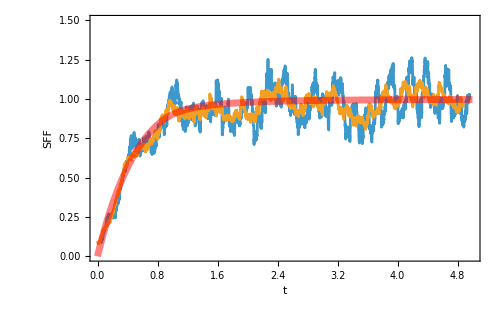

```mathematica
n=Length[eigvals];
data=Table[{t,SFF[unfoldedeigvals,tH*t]/n},{t,0.005,5,0.001}];

Show[
ListPlot[{MovingAverage[data,80],ExponentialMovingAverage[data,0.008]},Joined->True,PlotRange->{{0,5},{0,1.5}},Frame->True,FrameStyle->Directive[Black,FontSize->22],FrameLabel->{HoldForm@, }],
Plot[GOESFF[t],{t,0,5},PlotStyle->Directive[Red,Thickness[0.01],Opacity[0.5]],PlotRange->All],
ImageSize->500
]
```

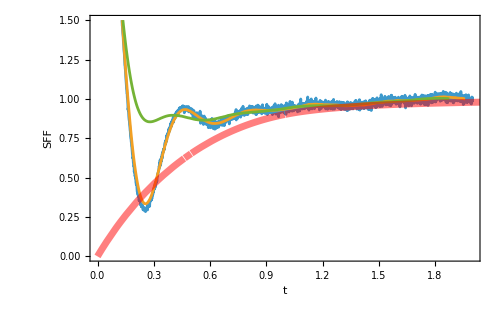

```mathematica
data=Table[{t,1+Total[Cos[Differences[unfoldedeigvals,1,#]*tH*t]&/@Range[5],2]/n},{t,0.005,2,0.001}];
Show[
ListPlot[{data,MovingAverage[data,80],ExponentialMovingAverage[data,0.008]},Joined->True,PlotRange->{All,{0,1.5}},Frame->True,FrameStyle->Directive[Black,FontSize->22],FrameLabel->{HoldForm@, }],
Plot[GOESFF[t],{t,0,5},PlotStyle->Directive[Red,Thickness[0.01],Opacity[0.5]],PlotRange->All],
ImageSize->500
]
```

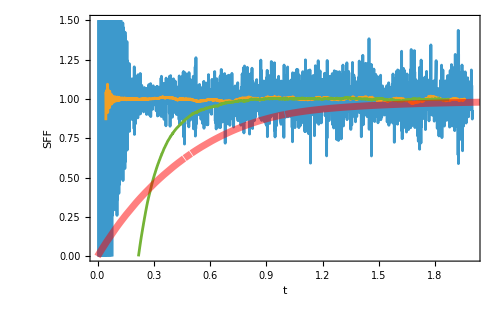

```mathematica
data=Table[{t,1+Total[Cos[Differences[unfoldedeigvals,1,#]*tH*t]&/@Range[1000,1200],2]/n},{t,0.005,2,0.001}];
Show[
ListPlot[{data,MovingAverage[data,80],ExponentialMovingAverage[data,0.008]},Joined->True,PlotRange->{All,{0,1.5}},Frame->True,FrameStyle->Directive[Black,FontSize->22],FrameLabel->{HoldForm@, }],
Plot[GOESFF[t],{t,0,5},PlotStyle->Directive[Red,Thickness[0.01],Opacity[0.5]],PlotRange->All],
ImageSize->500
]
```

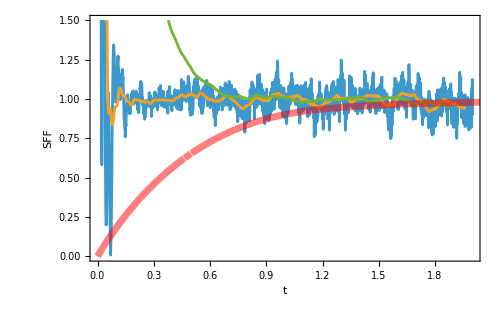

```mathematica
data=Table[{t,1+Total[Cos[Differences[unfoldedeigvals,1,#]*tH*t]&/@Range[2000,2100],2]/n},{t,0.005,2,0.001}];
Show[
ListPlot[{data,MovingAverage[data,80],ExponentialMovingAverage[data,0.008]},Joined->True,PlotRange->{All,{0,1.5}},Frame->True,FrameStyle->Directive[Black,FontSize->22],FrameLabel->{HoldForm@, }],
Plot[GOESFF[t],{t,0,5},PlotStyle->Directive[Red,Thickness[0.01],Opacity[0.5]],PlotRange->All],
ImageSize->500
]
```

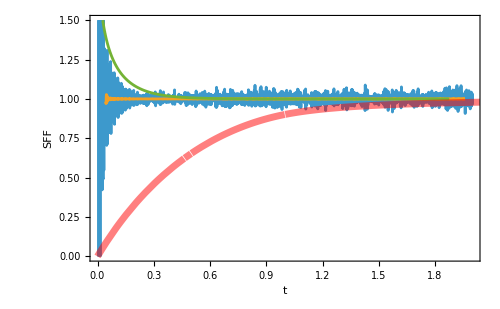

```mathematica
data=Table[{t,1+Total[Cos[Differences[unfoldedeigvals,1,#]*tH*t]&/@Range[4500,4600],2]/n},{t,0.005,2,0.001}];
Show[
ListPlot[{data,MovingAverage[data,80],ExponentialMovingAverage[data,0.008]},Joined->True,PlotRange->{All,{0,1.5}},Frame->True,FrameStyle->Directive[Black,FontSize->22],FrameLabel->{HoldForm@, }],
Plot[GOESFF[t],{t,0,5},PlotStyle->Directive[Red,Thickness[0.01],Opacity[0.5]],PlotRange->All],
ImageSize->500
]
```